```mathematica
Clear["`*"]
```

```mathematica
f[n_]:=(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]
d[p_]:=1/#&@Simplify[Sum[n f[n],{n,1,p-1}]+f[p]/c]
1/#&/@d@5//RepeatedTiming
```

{0.000095,5-20 c+48 c^2-56 c^3+24 c^4}

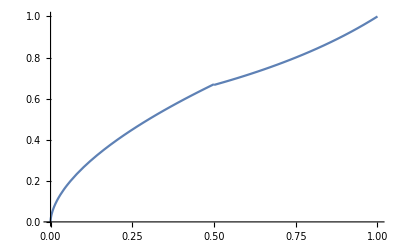

Piecewise[{{1/(5-20 c+48 c^2-56 c^3+24 c^4), 1/5<c<1/4}, {1/(4-10 c+13 c^2-6 c^3), 1/4<c<1/3}, {1/(3-4 c+2 c^2), 1/3<c<1/2}, {1/(2-c), 1/2<c<1}, {0, True}}]

```mathematica
Plot[Piecewise[{{c^(1/(√3)),0≤c≤1/2},{1/(2-c),1/2<c≤1}},0],{c,0,1}]
```

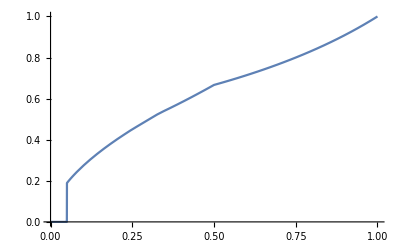

```mathematica
Plot[Piecewise[Function[{a,b,d},{a,b<c<d}]@@@Table[{d[i],1/i,1/(i-1)},{i,20,2,-1}]],{c,0,1}]
```

{{0.05,0.00380099},{0.1,0.0147458},{0.15,0.0322209},{0.2,0.055704},{0.25,0.0847441},{0.3,0.118949},{0.35,0.157983},{0.4,0.201547},{0.45,0.249304},{0.5,0.302103},{0.55,0.360398},{0.6,0.42265},{0.65,0.481125},{0.7,0.571429},{0.75,0.666667},{0.8,0.75},{0.85,0.823529},{0.9,0.888889},{0.95,0.947368}}

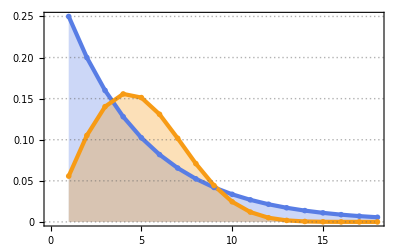

```mathematica
(*$Assumptions={0≤c≤1,Element[n,Integers]};
sol={p[n]==c*n*(1-Sum[p[i],{i,1,n-1}]),p[1]==c};
ans=RSolveValue[sol,p[n],n];*)(*p[1]:=c;p[n_]:=n c (1-Sum[p[i],{i,1,n-1}]);Factor[p/@Range[10]];
ans=c*(-1)^(n+1)*n*Product[c*i-1,{i,1,n-1}];*)f[c_]:=Table[{n,(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]},{n,1,1/c}]
g[c_]:=Chop[Insert[f[c],{Ceiling[1/c],1-Total[Transpose[f[c]][[2]]]},-1]]
h[c_]:=1/Total[(#1[[1]]*#1[[2]]&)[Transpose[If[1/Rationalize[c]//IntegerQ,f[c],g[c]]]]]
fun=Interpolation[Table[{i,h[i]},{i,0.001,1,0.001}]];
Table[{i,InverseFunction[fun]@i},{i,0.05,0.95,0.05}]
(*p[1]:=c;p[n_]:=c(1-Sum[p[i],{i,1,n-1}]);
Factor[p/@Range[10]] foo[n_]:=c*(1-c)^(n-1) Factor[foo/@Range[10]]*)
bar[c_]:=Chop@Table[c*(1-c)^(n-1),{n,0,Length[g[InverseFunction[fun]@c]]-1}];
baz[c_]:=ListLinePlot[{bar[c],(g[InverseFunction[fun]@c]//Transpose)[[2]]},Filling->Axis,AxesOrigin->{1,0},PlotTheme->"Business"]
baz[0.2]
```

```mathematica
c^(1/(√3))-fun
```

InterpolatingFunction[{{0.001, 1.}}, <>]

InterpolatingFunction::dmval: 输入值 {0.0000102143} 位于插值函数的数据范围之外. 将使用外推法.

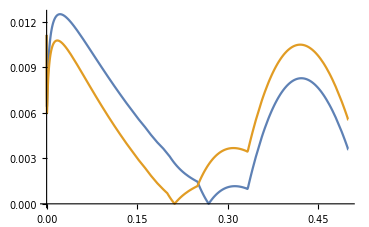

```mathematica
Plot[{Abs[c^EulerGamma-fun[c]],Abs[c^0.573-fun[c]]},{c,0,0.5}]
```

```mathematica
FindFit[Table[{i,h[i]},{i,0.001,0.5,0.001}],a+x^b,{a,b},x]
```

{a→-0.00100186,b→0.573042}

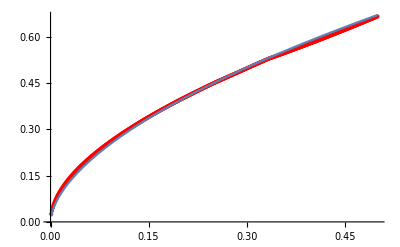

```mathematica
Show[ListPlot[Table[{i,h[i]},{i,0.001,0.5,0.001}],PlotStyle->Red],Plot[a+x^b/.{a->-0.0010018586762235077,b->0.5730418649124949},{x,0.001,0.5}]]
```

```mathematica
Sqrt[2.0]/2
```

0.707107

```mathematica
HarmonicNumber[n]>1
```

HarmonicNumber[n]>1

```mathematica
Clear["`*"]
fact[n_]:=fact[n-1]+fact[n-2];fact[1]=fact[2]=1;fact[10]
```

55